1/3

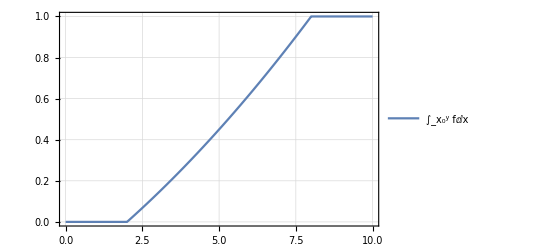

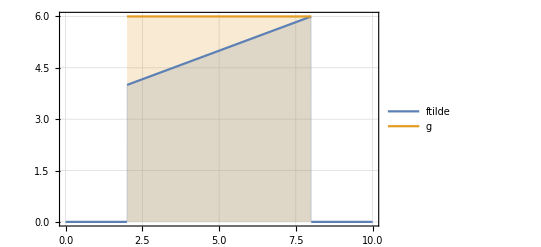

```mathematica
Subscript[x, 0]=2;
Subscript[x, 1]=8;
Subscript[y, 0]=4;
Subscript[y, 1]=6;

Subscript[m, 0]=(Subscript[y, 1]-Subscript[y, 0])/(Subscript[x, 1]-Subscript[x, 0])
Subscript[a, 0]=(Subscript[y, 0]+Subscript[y, 1])(Subscript[x, 1]-Subscript[x, 0])/2;

Subscript[y, m]=Max[Subscript[y, 0],Subscript[y, 1]];

ftilde= Piecewise[{{0, x<Subscript[x, 0]}, {0, x>Subscript[x, 1]}}, Subscript[m, 0](x-Subscript[x, 0])+Subscript[y, 0]];
f= Piecewise[{{0, x<Subscript[x, 0]}, {0, x>Subscript[x, 1]}}, (Subscript[m, 0](x-Subscript[x, 0])+Subscript[y, 0])/Subscript[a, 0]];
g= Piecewise[{{zzz, x<Subscript[x, 0]}, {zzz, x>Subscript[x, 1]}}, Subscript[y, m]];

Plot[∫_Subscript[x, 0]^y fⅆx,{y,0,10},PlotTheme->"Detailed"]

Plot[{ftilde,g},{x,0,10}, PlotTheme->"Detailed",Filling->Axis]
```